# 第六章

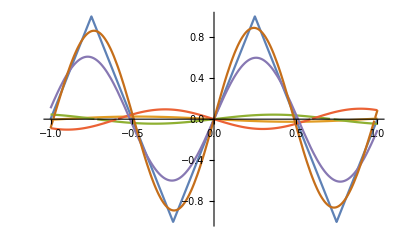

```mathematica
f[x_]:=TriangleWave[x]
Plot[{f[x],Evaluate[Table[Normal[FourierSeries[f[x],x,n]],{n,3,7,1}]]},{x,-1,1}]
```

```mathematica
f[x_,y_]=UnitBox[x,y];
f2=FourierTransform[f[x,y],{x,y},{w1,w2}]
Plot3D[f2,{w1,-10,10},{w2,-10,10},PlotRange->All]
```

(2 Sin[w1/2] Sin[w2/2])/(π w1 w2)

-Graphics3D-

```mathematica
f[x_]:=Piecewise[{{-1,-1<x<0},{1,0<=x<=1},{0,True}}];
FourierTransform[f[x],x,ω]
```

-(ⅈ √(2/π) (-1+Cos[ω]))/ω

```mathematica
Clear["`*"];
f[x_]:=Piecewise[{{Sin[x],-Pi<=x<=Pi}},0];
FourierTransform[f[x],t,ω]
Integrate[Sin[ω Pi] Sin[ω t]/(1-ω^2),{ω,0,Infinity}]
```

√(2 π) DiracDelta[ω] (Piecewise[{{Sin[x], -π≤x≤π}, {0, True}}])

ConditionalExpression[1/4 π (1/Sign[π-t]+1/Sign[π+t]) Sin[t], t∈ℝ]

```mathematica
Clear["`*"];
f[t_]:=DiracDelta[t-1] (t-2)^2 Cos[t];
FourierTransform[f[t],t,ω]
```

(ⅇ^(ⅈ ω) Cos[1])/(√(2 π))

```mathematica
Clear["`*"];
FourierTransform[Sin[5 t+Pi/3],t,ω]
```

1/2 ⅈ √(π/2) DiracDelta[-5+ω]+1/2 √((3 π)/2) DiracDelta[-5+ω]-1/2 ⅈ √(π/2) DiracDelta[5+ω]+1/2 √((3 π)/2) DiracDelta[5+ω]

```mathematica
FourierTransform[t^2 Cos[t],t,ω]
```

-√(π/2) DiracDelta''[-1+ω]-√(π/2) DiracDelta''[1+ω]

```mathematica
FourierTransform[Sin[w t] HeavisideTheta[t],t,ω]
```

-1/(2 √(2 π) (-w+ω))+1/(2 √(2 π) (w+ω))+1/2 ⅈ √(π/2) DiracDelta[-w+ω]-1/2 ⅈ √(π/2) DiracDelta[w+ω]

```mathematica
FourierTransform[E^(I t) HeavisideTheta[t-2],t,ω]
```

(ⅈ ⅇ^(2 ⅈ (1+ω)))/(√(2 π) (1+ω))+√(π/2) DiracDelta[1+ω]